```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
data=Import["exports/dr9_dr10_match.csv"];
```

```mathematica
dr9=data[[All,{1,2,3}]];
dr10=data[[All, {4,5,6}]];
diff=dr9[[All,{1,2,3}]]-dr10[[All,{1,2,3}]];
error=Table[{
ErrorBar[diff[[i]][[1]]],
ErrorBar[diff[[i]][[2]]],
ErrorBar[diff[[i]][[3]]]
},{i,1,Length[diff]}];
dataErr={dr9[[All,{1,2}]], error[[All, 3]]}//Transpose;
dist=Table[
EuclideanDistance[
{dr9[[i, 1]], dr9[[i, 2]], 0},
{dr10[[i, 1]], dr10[[i, 2]], 0}], 
{i,1,Length[data]}];
```

```mathematica
ErrorListPlot[
dataErr,
PlotRange->All,
AxesLabel->{"RA","DEC"},
PlotLabel->"RA vs DEC w/ error in z fron DR9 -> DR10"
]
```

-Graphics-

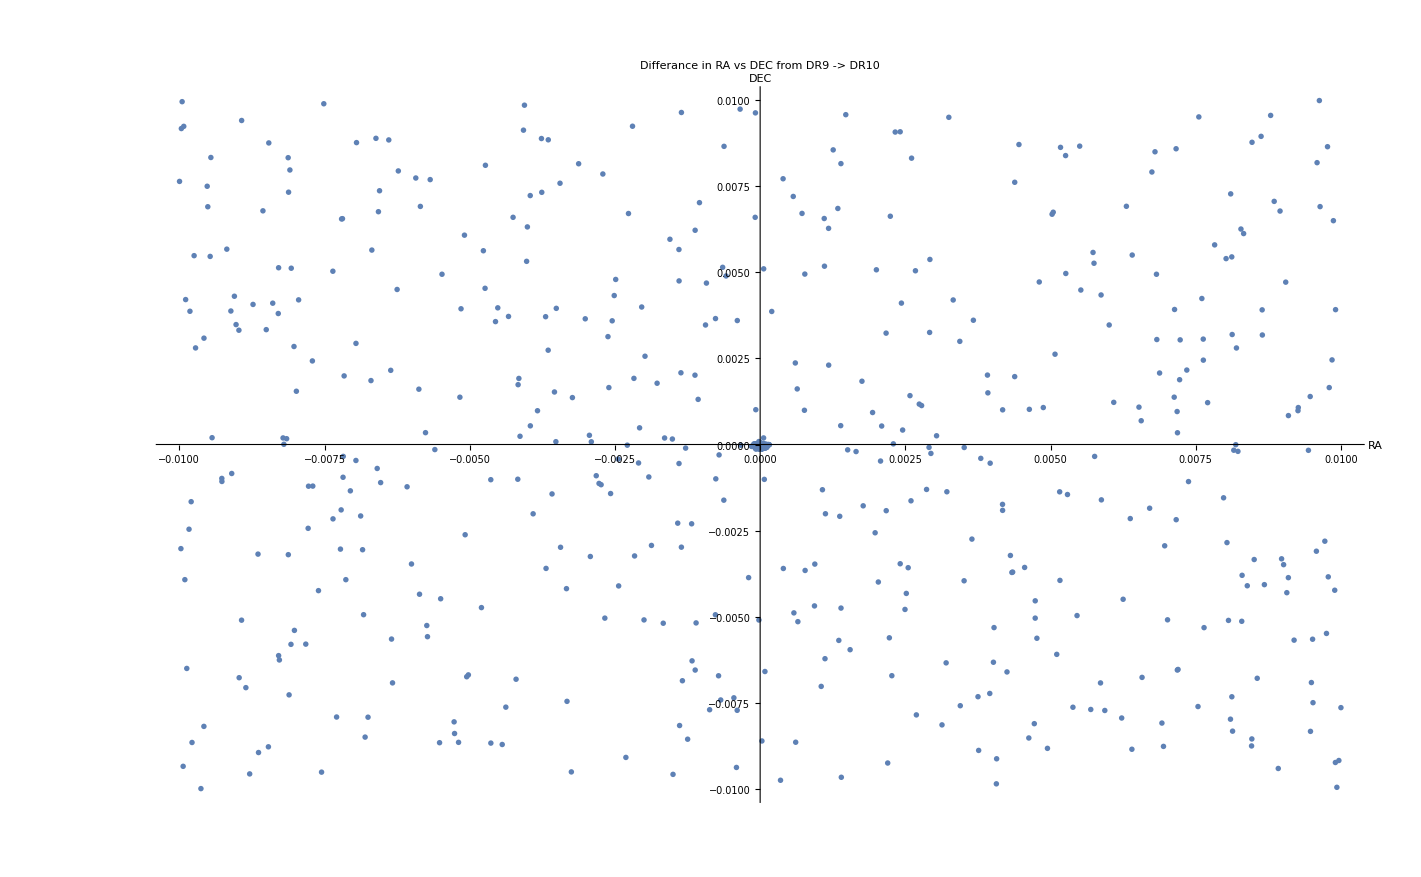

```mathematica
ListPlot[
diff[[All,{1,2}]],
PlotRange->All,
AxesLabel->{"RA","DEC"},
PlotLabel->"Differance in RA vs DEC from DR9 -> DR10"
]
```

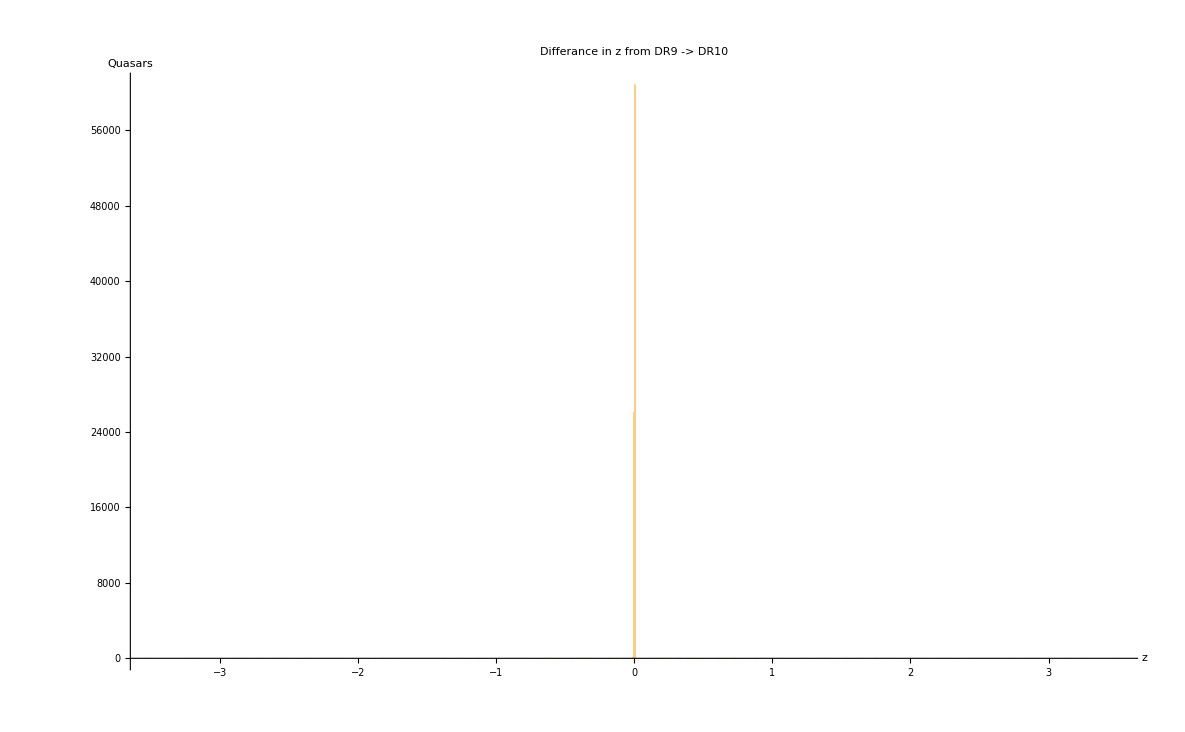

```mathematica
Histogram[
diff[[All,3]],1000,
PlotRange->All,
AxesLabel->{"z", "Quasars"},
PlotLabel->"Differance in z from DR9 -> DR10"
]
```

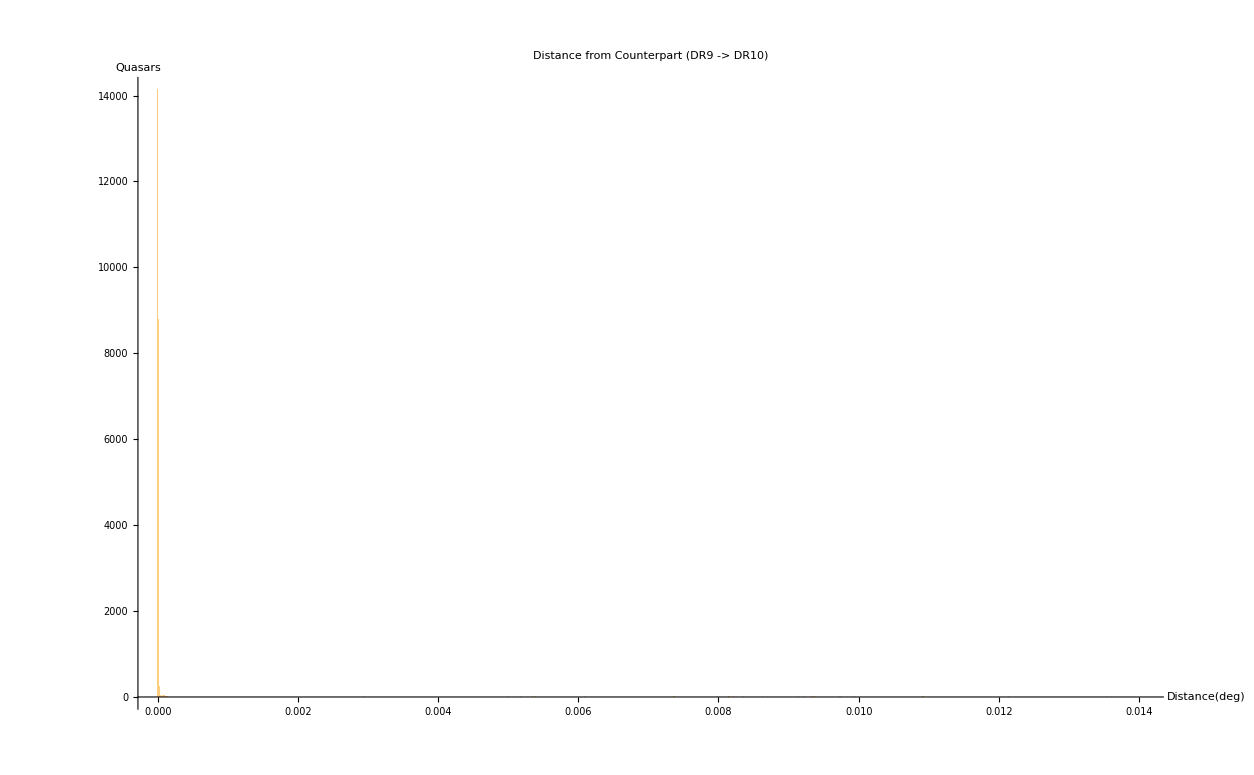

```mathematica
Histogram[
dist,
PlotRange->All,
AxesLabel->{"Distance(deg)","Quasars" },
PlotLabel->"Distance from Counterpart (DR9 -> DR10)"
]
```

```mathematica
Mean[dr10[[All,3]]]
Mean[dr9[[All,3]]]
```

2.2245

2.22453

```mathematica
match=Table[
Line[{dr9[[i, {1,2}]],dr10[[i,{1,2}]]}],
{i,1,Length[dr9]}
]
```

{Line[{{0.008067,-0.240971},{0.00806797,-0.240974}}],Line[{{0.013229,1.25297},{0.0132383,1.25296}}],Line[{{0.019223,3.85623},{0.0192244,3.85623}}],Line[{{0.020696,-0.278343},{0.0206977,-0.278347}}],Line[{{0.020929,-0.641393},{0.0209319,-0.641397}}],87431,Line[{{359.979,1.93936},{359.979,1.93936}}],Line[{{359.982,-1.2359},{359.982,-1.23591}}],Line[{{359.988,-0.378832},{359.988,-0.378831}}],Line[{{359.994,0.430948},{359.994,0.430949}}],Line[{{359.996,2.81855},{359.996,2.81855}}]}
 |  |  |  |